Лабораторная работа 6

Математические модели процессов нелинейной
теплопроводности и горения. Вариант 5

Параметры задачи

```mathematica
σ=2.5;
k0=2.0;
c=3;
t0=0;
tmax=0.5;
h=0.02;
τ=2 10^-4;
smax=IntegerPart[tmax/τ];
n=100;
x1=1;
uex[x_,t_]=((σ(x1-x)^2)/(2k0(σ+2)(c-t)))^(1/σ)
```

0.454012 ((1-x)^2/(3-t))^0.4

```mathematica
eqn[s_,k_]:= Table[(yk[k+1,i]-y[s,i])/τ==1/h (k*((yk[k,i+1]-yk[k,i])/2) (yk[k+1,i+1]-yk[k+1,i])/h- k*((yk[k,i]-yk[k,i-1])/2)(yk[k+1,i]-yk[k+1,i-1])/h),{i,1,n-1}]
Y[s_, k_]:=Table[yk[k, i],{i,1,n-1}];
```

Точное решение

```mathematica
pot[t_]:=Plot[uex[x,t],{x,0,h n},PlotRange-> All]
Manipulate[pot[t],{t,t0,tmax}]
```

Метод сквозного счета

$Aborted

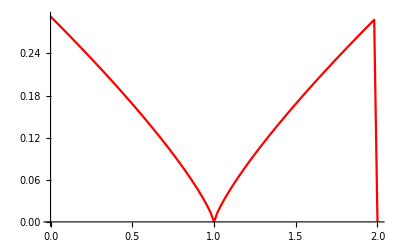

```mathematica
Clear[y];
Do [y[i,0]=uex[i h, 0],{i,1,n-1}] 
Do[y[0,s]=uex[0,s*τ]; y[n,s]=uex[2,s*τ], {s,0,smax}]

Do [
Clear[yk];
Do[yk[0,i]=y[i,s];yk[1,i]=yk[0,i];,{i,0,n}];
yk[1,1]=yk[0,i]+0.0003;
k=1;
enot=Table[Abs[yk[i,k]-yk[i,k-1]], {i,0,n}, {s,0,smax}];
megaenot=Max[enot];
While[megaenot≥ϵ,
k++;
yk[k,0]=y[0,s];
yk[k,n]=y[n,s];

{B,A}=CoefficientArrays[eqn[s,k-1], Y[s+1,k]];yy = LinearSolve [A,-B];Do[yk[k,i]=yy[[i]],{i,1,n-1}];
enot=Table[Abs[yk[i,k]-yk[i,k-1]], {i,0,n}, {s,0,smax}];
megaenot=Max[enot];];
For[i=0,i≤ n,i++,y[i,s+1]=yk[k,i]];,{s,0,smax-1}]
ListPlot[Table[{i*h,y[i,0]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]]
```

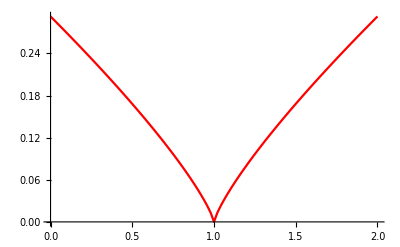

```mathematica
Clear[y];
Do [y[i,0]=uex[i h, 0],{i,1,n-1}] 
Do[y[0,s]=uex[0,s*τ]; y[n,s]=uex[2,s*τ], {s,0,smax}]

s=0;
Clear[yk];
Do[yk[0,i]=y[i,s];yk[1,i]=yk[0,i];,{i,0,n}];
yk[1,1]=yk[0,i]+0.0003;
k=1;
enot=Table[Abs[yk[i,k]-yk[i,k-1]], {i,0,n}, {s,0,smax}];
megaenot=Max[enot];

k++;
yk[k,0]=y[0,s];
yk[k,n]=y[n,s];

{B,A}=CoefficientArrays[eqn[s,k-1], Y[s+1,k]];yy = LinearSolve [A,-B];Do[yk[k,i]=yy[[i]],{i,1,n-1}];
enot=Table[Abs[yk[i,k]-yk[i,k-1]], {i,0,n}, {s,0,smax}];
megaenot=Max[enot];
For[i=0,i≤ n,i++,y[i,s+1]=yk[k,i]]
ListPlot[Table[{i*h,y[i,0]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]]
```

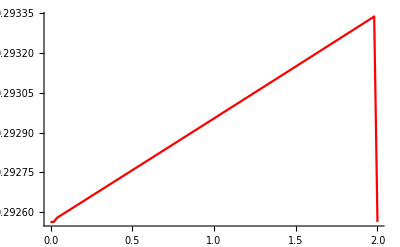

```mathematica
k++;
yk[k,0]=y[0,s];
yk[k,n]=y[n,s];

{B,A}=CoefficientArrays[eqn[s,k-1], Y[s+1,k]];yy = LinearSolve [A,-B];Do[yk[k,i]=yy[[i]],{i,1,n-1}];
enot=Table[Abs[yk[i,k]-yk[i,k-1]], {i,0,n}, {s,0,smax}];
megaenot=Max[enot];
For[i=0,i≤ n,i++,y[i,s+1]=yk[k,i]]
ListPlot[Table[{i*h,yk[k,i]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]]
```